# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Entropy\Eigenvectors_h_0

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\packages\\QMB - Copy.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
Clear[U];
U[t_]:=MatrixExp[-I*H*t];
```

# All together

## Plots

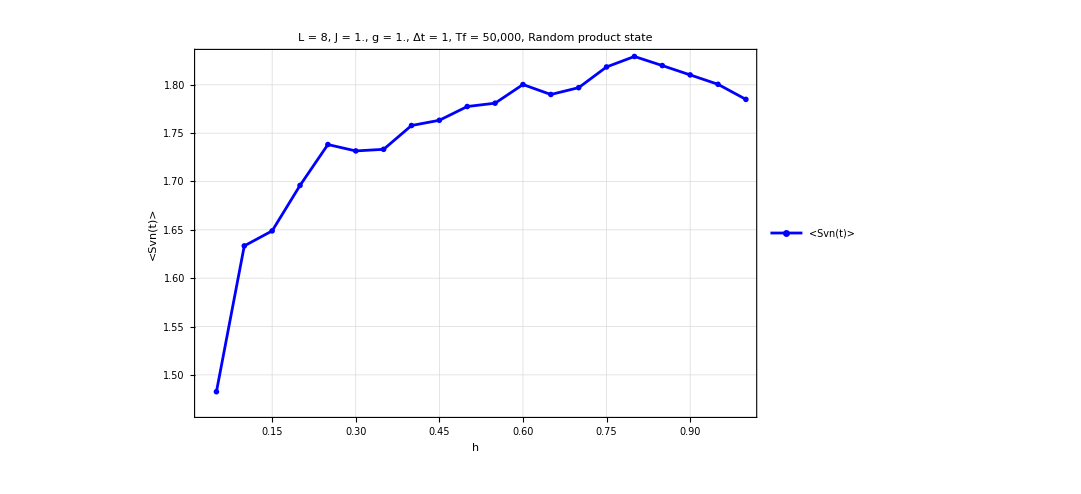

```mathematica
ListPlot[meanentropies,PlotRange->All,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["<Svn(t)>"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Blue},PlotLegends->{"<Svn(t)>"}]
```

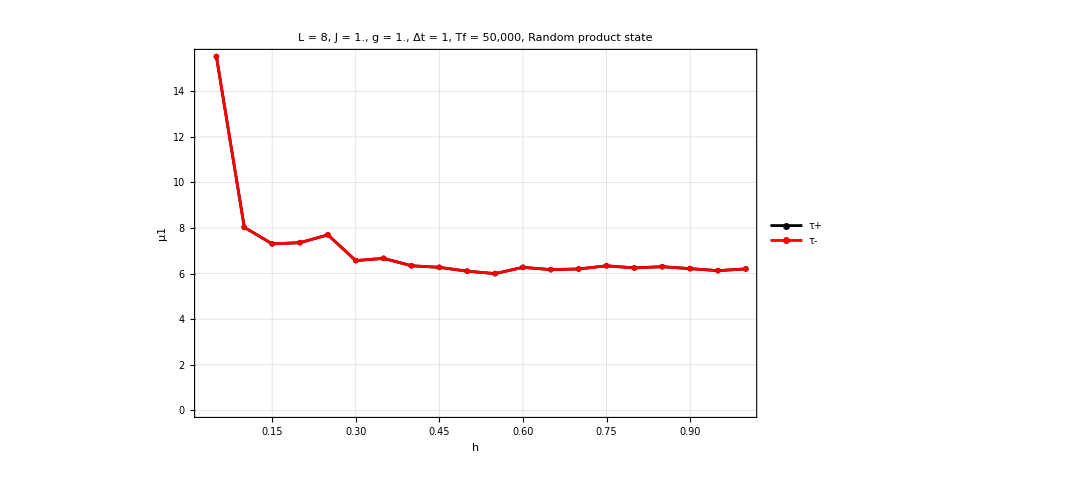

```mathematica
ListPlot[{Transpose[{datap[[All,1]],datap[[All,2]]}],Transpose[{datam[[All,1]],datam[[All,2]]}]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["μ1"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Black,Red},PlotLegends->{"τ+","τ-"}]
```

std=μ2  =(1/(n-1)∑_(i=1)^n (x_i-μ̂ 1)^2)^(1/2)

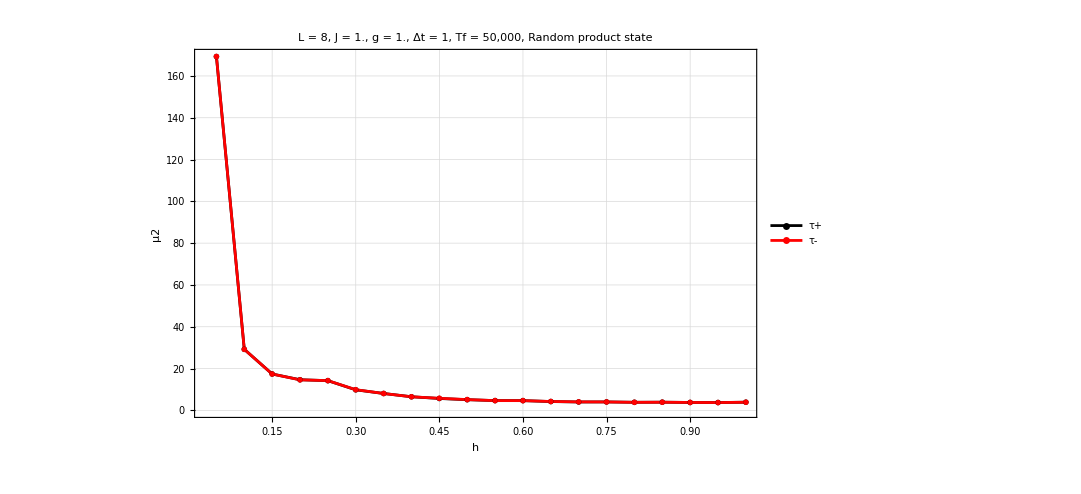

```mathematica
ListPlot[{Transpose[{datap[[All,1]],datap[[All,3]]}],Transpose[{datam[[All,1]],datam[[All,3]]}]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>", Tf = 50,000, Random product state",20,Black],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{Style["h"],Style["μ2"]},FrameStyle->Directive[Black,FontSize->30],ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{Black,Red},PlotLegends->{"τ+","τ-"}]
```

## Eigenvectors h=0

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[svn];
svn[ini_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ},
rho=MatrixPartialTrace[Dyad[state,state],2,{2^(L/2),2^(L/2)}];
λ=Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
Δt=1;
tlist=Range[0,5(10^4),Δt];
tlist//Length
```

50001

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=0.05;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
energytest=ParallelTable[Chop[i.H.i],{i,eigenvectest}];
sortedEigenvectors=SortBy[Transpose[{energytest,eigenvectest}],First][[All,2]];
data=Sort[energytest];
uniqueElements=DeleteDuplicates[data];
colors=Table[RGBColor[0.8(i/Length[uniqueElements]),0.5(1-i/Length[uniqueElements]),1-i/Length[uniqueElements]],{i,Length[uniqueElements]}];
index=Flatten[DeleteDuplicatesBy[MapIndexed[{#1,#2}&,data],First][[All,2]]];
eigenvectors=Table[sortedEigenvectors[[i]],{i,index}];
```

```mathematica
entropies=ParallelTable[{t,svn[i,t]},{i,eigenvectors},{t,tlist},DistributedContexts->Full];
```

```mathematica
entropies//Dimensions
```

{11,1001,2}

```mathematica
plots=Table[Show[ListPlot[entropies[[i]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt]<>" , E = "<>ToString[uniqueElements[[i]]],20,Black],PlotStyle->colors[[i]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All],Plot[Mean[entropies[[i]]],{x,0,Length[tlist]},PlotStyle->Directive[Dashed,colors[[i]]]],AspectRatio->1/2,ImageSize->1200],{i,Length[entropies]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
Export["entropy_eigenvecs_h_0_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[hx]<>".m",entropies]
```

```mathematica
hlist=Range[0.05,1.0,0.05];
```

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
Do[

Clear[eigenval,eigenvec];
H=IsingNNOpenHamiltonian[h,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
energytest=ParallelTable[Chop[i.H.i],{i,eigenvectest},DistributedContexts->Full];
sortedEigenvectors=SortBy[Transpose[{energytest,eigenvectest}],First][[All,2]];
data=Sort[energytest];
uniqueElements=DeleteDuplicates[data];
(*colors=Table[RGBColor[0.8(i/Length[uniqueElements]),0.5(1-i/Length[uniqueElements]),1-i/Length[uniqueElements]],{i,Length[uniqueElements]}];*)
index=Flatten[DeleteDuplicatesBy[MapIndexed[{#1,#2}&,data],First][[All,2]]];
eigenvectors=Table[sortedEigenvectors[[i]],{i,index}];
entropies=ParallelTable[{t,svn[i,t]},{i,eigenvectors},{t,tlist},DistributedContexts->Full];
Export["entropy_eigenvecs_h_0_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[h]<>".m",entropies];
Export["energytest_eigenvecs_h_0_L_"<>ToString[L]<>"_g_"<>ToString[hz]<>"_h_"<>ToString[h]<>".m",energytest];

,{h,hlist}];
```

```mathematica
Δt=1;
tlist=Range[0,5(10^4),Δt];
tlist//Length
```

50001

```mathematica
hlist=Range[0.05,0.4,0.05];
```

```mathematica
allentropies=Table[Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\Eigenvectors_h_0\\entropy_eigenvecs_h_0_L_8_g_1._h_"<>ToString[h]<>".m"],{h,hlist}];
```

```mathematica
allentropies//Dimensions
```

{8,11,50001,2}

```mathematica
allenergies=Table[Import["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Entropy\\Eigenvectors_h_0\\energytest_eigenvecs_h_0_L_8_g_1._h_"<>ToString[h]<>".m"],{h,hlist}];
```

```mathematica
allenergies//Dimensions
```

{8,256}

```mathematica
uniques={};
Do[
data=Sort[allenergies[[i]]];
uniqueElements=DeleteDuplicates[data];
AppendTo[uniques,uniqueElements];
,{i,Length[hlist]}]
```

## Plots

```mathematica
L=8;
hx=0;
J=1.;
hz=1.0;
Htest=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvaltest,eigenvectest}=Transpose[Sort[Transpose[Eigensystem[N[Htest]]]]];
```

```mathematica
L=8;
hx=0.4;
J=1.;
hz=1.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
neweigenvectest=Table[Conjugate[eigenvec].i,{i,eigenvectest}];
iprtest=Table[Total[Abs[i]^4],{i,neweigenvectest}];
```

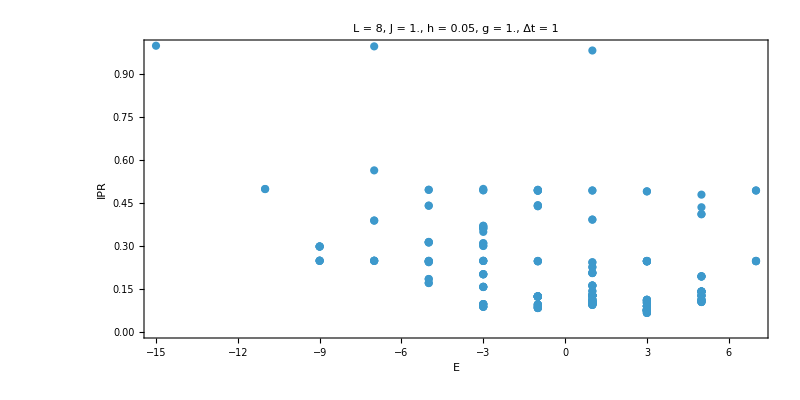

```mathematica
ListPlot[Transpose[{energytest,iprtest}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["IPR"]},AspectRatio->1/2,ImageSize->800,PlotRange->All]
```

```mathematica
q=1;
ListPlot[allentropies[[q]][[All]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q]]]
```

-Graphics-

```mathematica
q=1;
plots=Table[ListPlot[allentropies[[q]][[i]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors[[i]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q,i]]],{i,11}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

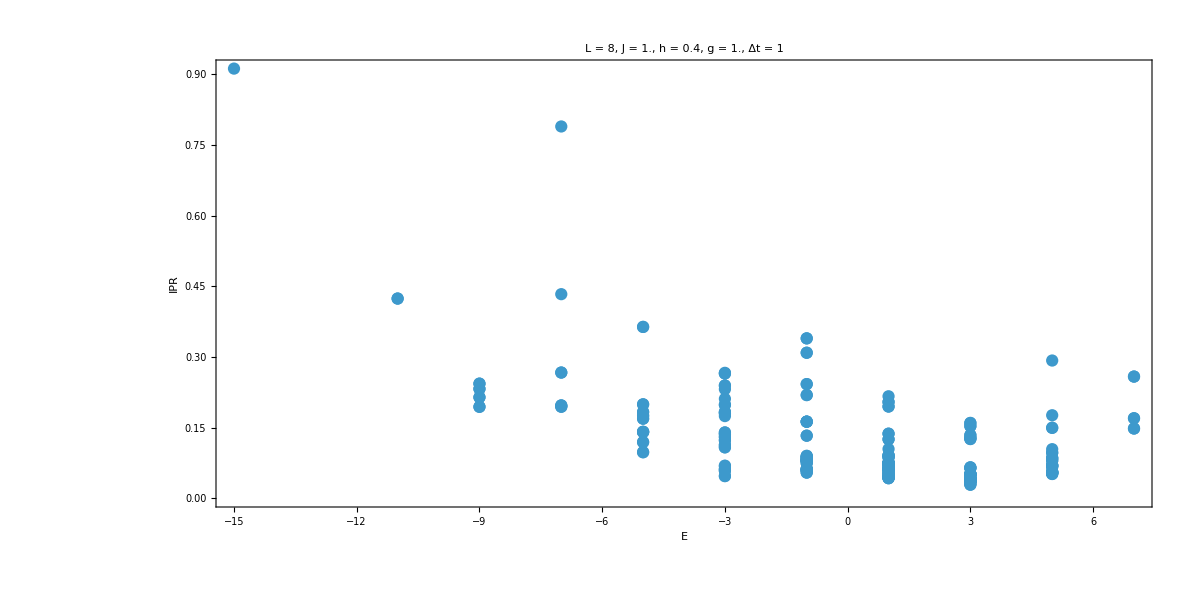

```mathematica
ListPlot[Transpose[{Sort[energytest],iprtest}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hx]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["IPR"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All]
```

```mathematica
q=-1;
ListPlot[allentropies[[q]][[All]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q]]]
```

-Graphics-

```mathematica
q=-1;
plots=Table[ListPlot[allentropies[[q]][[i]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[hlist[[q]]]<>", g = "<>ToString[hz]<>", Δt = "<>ToString[Δt],20,Black],PlotStyle->colors[[i]],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},AspectRatio->1/2,ImageSize->1200,PlotRange->All,PlotLegends->uniques[[q,i]]],{i,11}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```